```mathematica
data0=Import["C:\\Users\\Jason Smith\\Desktop\\ECONDATA\\state_of_industry_data.xls"][[1]];
```

```mathematica
data0[[1,3]]
```

Tue 18 Feb 2020 00:00:00GMT-7.

```mathematica
lengthYear=365.2425;
```

```mathematica
Cases[data0,x_/;x[[2]]=="Seattle"][[1]]
data ={((1900+FromDate[DateList[#[[1]]]]/(lengthYear*3600*24))-2020)*lengthYear,#[[2]]}&/@Drop[Transpose[{Take[data0[[1,All]],Length[%]],%}],2]
```

{city,Seattle,8.,11.,6.,1.,1.,12.,1.,0.,3.,5.,7.,0.,-18.,-29.,-31.,-31.,-36.,-34.,-35.,-25.,-47.,-49.,-54.,-58.,-63.,-63.,-62.,-83.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.}

{{47.9,8.},{48.9,11.},{49.9,6.},{50.9,1.},{51.9,1.},{52.9,12.},{53.9,1.},{54.9,0.},{55.9,3.},{56.9,5.},{57.9,7.},{58.9,0.},{59.9,-18.},{60.9,-29.},{61.9,-31.},{62.9,-31.},{63.9,-36.},{64.9,-34.},{65.9,-35.},{66.9,-25.},{67.9,-47.},{68.9,-49.},{69.9,-54.},{70.9,-58.},{71.9,-63.},{72.9,-63.},{73.9,-62.},{74.9,-83.},{75.9,-100.},{76.9,-100.},{77.9,-100.},{78.9,-100.},{79.9,-100.},{80.9,-100.},{81.9,-100.},{82.9,-100.},{83.9,-100.},{84.9,-100.},{85.9,-100.},{86.9,-100.},{87.9,-100.},{88.9,-100.},{89.9,-100.},{90.9,-100.},{91.9,-100.},{92.9,-100.},{93.9,-100.},{94.9,-100.},{95.9,-100.},{96.9,-100.},{97.9,-100.},{98.9,-100.},{99.9,-100.},{100.9,-100.},{101.9,-100.},{102.9,-100.},{103.9,-100.},{104.9,-100.}}

## fit to data

```mathematica
fitFunc=a0/(1+Exp[(t-t0)/b0])+a1/(1+Exp[(t-t1)/b1])-100
```

-100+a0/(1+ⅇ^((t-t0)/b0))+a1/(1+ⅇ^((t-t1)/b1))

```mathematica
nlm=NonlinearModelFit[data,fitFunc,
{
{a0,60},{b0,4.},{t0,65.},
{a1,40.},{b1,0.5},{t1,70.}
},
t]
```

FittedModel[-100+34.7134/(1+ⅇ^(5.68135 (-«18»+t)))+75.4817/(1+ⅇ^(0.256269 (-63.2208+t)))]

```mathematica
transitions={t0,t1}/.nlm["BestFitParameters"]
widths={b0,b1}/.nlm["BestFitParameters"]
```

{63.2208,74.8171}

{3.90215,0.176015}

```mathematica
levels={a0+a1-100,a1-100}/.nlm["BestFitParameters"]
```

{10.1951,-65.2866}

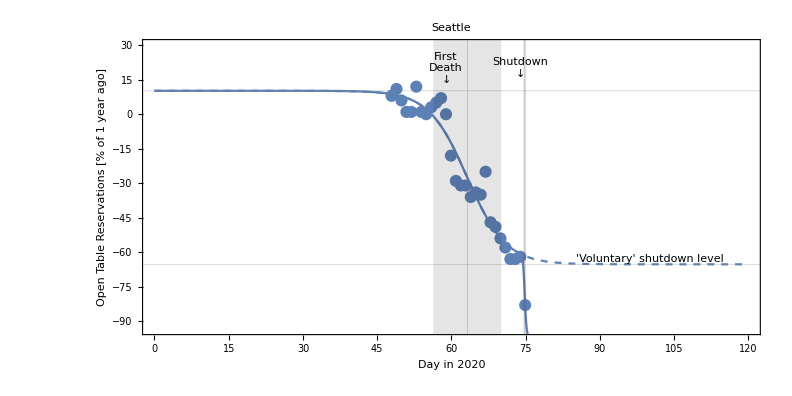

```mathematica
Show[Plot[{Normal[nlm]},{t,0,120}],Plot[a0/(1+Exp[(t-t0)/b0])+a1/1-100/.nlm["BestFitParameters"],{t,0,120},PlotStyle->Dashed],ListPlot[data],PlotRange->{-93.4,30},GridLines->{Join[transitions],levels},ImageSize->11*72,AspectRatio->1/2,Frame->{True,True,False,False},Axes->False,
Epilog->{
Text["'Voluntary' shutdown level",{100,a1-100/.nlm["BestFitParameters"]},{0,-1}],
Text["\nShutdown\n↓",{((1900+FromDate[{2020,3,15,0,0,0}]/(lengthYear*3600*24))-2020)*lengthYear,20}],
Text["First\nDeath\n↓",{((1900+FromDate[{2020,2,29,0,0,0}]/(lengthYear*3600*24))-2020)*lengthYear,20}],
Opacity[0.1],MapThread[Rectangle[{#1+Log[3+2 √2]#2,-150},{#1-Log[3+2 √2]#2,50}]&,{transitions,widths}]},BaseStyle->FontSize->15,FrameLabel->{"Day in 2020\n","\nOpen Table Reservations [% of 1 year ago]"},PlotLabel->"\nSeattle"]
```